```mathematica
WebImageSearch["Downtown Los Angeles"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

```mathematica
ImageDimensions[%2]
```

{474,316}

```mathematica
EdgeDetect[Out[2]]
```

-Graphics-

```mathematica
Quantity[1,"Hours"]+Quantity[8,"Minutes"]+Quantity[55,"Seconds"]
```

4135 s

```mathematica
UnitConvert[Quantity[4135,"Seconds"],MixedUnit[{"Hours","Minutes","Seconds"}]]
```

1 8

```mathematica
Quantity[4135, "Seconds"]/2.5
```

1654. s

```mathematica
UnitConvert[Quantity[1654.,"Seconds"],MixedUnit[{"Minutes","Seconds"}]]
```

27 34.

-Graphics-

```mathematica
DiscreteWaveletPacketTransform[%9]
```

DiscreteWaveletData[<<DWPT>>, <4>, {4032, 3024}]

```mathematica
ImagePeriodogram[%9]
```

-Graphics-

```mathematica
ImageColorSpace[%9]
```

RGB

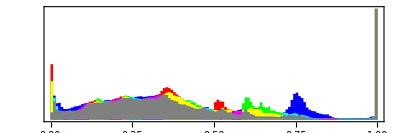

```mathematica
ImageHistogram[%9]
```

```mathematica
ColorConvert[%9,"Grayscale"]
```

-Graphics-

```mathematica
Binarize[%10]
```

-Graphics-

```mathematica
g=ReadList["ExampleData/fish.data",Number,RecordLists->True]
```

{{0.568627,0.576471,0.596078,0.615686,0.623529,0.611765,0.6,0.592157,0.584314,182,0.678431,0.686275,0.678431,0.678431,0.67451,0.670588,0.67451,0.686275,0.690196},199}
 |  |  |  |

```mathematica
Graphics[Raster[g]]
```

-Graphics-

```mathematica
ListConvolve[{{1,1,1},{1,-8,1},{1,1,1}},g]
```

{1}
 |  |  |  |

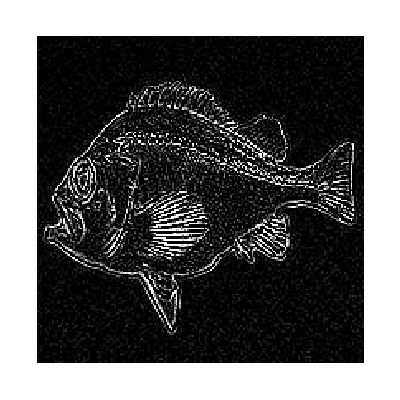

```mathematica
Graphics[Raster[Out[18]]]
```

```mathematica
Convolve[f[x]]
```

Convolve::argmu: Convolve called with 1 argument; 4 or more arguments are expected.

Convolve[f[x]]

```mathematica
Convolve[f,h,x,y]
```

Convolve[f,h,x,y]

```mathematica
Convolve[DiracDelta[x],f[x],x,y]
```

f[y]

```mathematica
Convolve[f[x],h,x,y]
```

Convolve[f[x],h,x,y]

```mathematica
Convolve[f[x],h[x],x,y]
```

Convolve[f[x],h[x],x,y]

```mathematica
Convolve[Exp[-x]UnitStep[x],Sin[x],x,y]
```

1/2 (-Cos[y]+Sin[y])

```mathematica
FullSimplify[ArcCurvature[{x,f[x]},x],{x,f[x],f'[x],f''[x]}∈Reals]
```

Abs[f''[x]]/((1+f'[x]^2)^(3/2))

```mathematica
Solve[Abs[f''[x]]/((1+f'[x]^2)^(3/2))==h[x],f'[x]]
```

{{f'[x]→-√(-1+Abs[f''[x]]^(2/3)/h[x]^(2/3))},{f'[x]→√(-1+Abs[f''[x]]^(2/3)/h[x]^(2/3))}}

```mathematica
√(-1+Abs[f''[x]]^(2/3)/h[x]^(2/3))
```

√(-1+Abs[f''[x]]^(2/3)/h[x]^(2/3))

```mathematica
D[f[x],x]==λ [x]f[x]
```

f'[x]==f[x] λ[x]

```mathematica
DSolve[f'[x]==f[x] λ[x],{f[x]},{x}]
```

{{f[x]→ⅇ^(λ[K[1]]K[1]1x) C[1]}}

```mathematica
Solve[D[f[x],x]==λ [x]f[x],λ[x]]
```

{{λ[x]→f'[x]/f[x]}}

```mathematica
Integrate[f[x]f'[x],{x,0,∞}]
```

∫_0^∞ f[x] f'[x]ⅆx

```mathematica
Integrate[Exp[x]x,{x,0,∞}]
```

Integrate::idiv: Integral of ⅇ^x x does not converge on {0,∞}.

∫_0^∞ ⅇ^x xⅆx

```mathematica
Integrate[Exp[-s x]x,{x,0,∞}]
```

ConditionalExpression[1/s^2,Re[s]>0]

```mathematica
Exp[-x]x
```

ⅇ^-x x

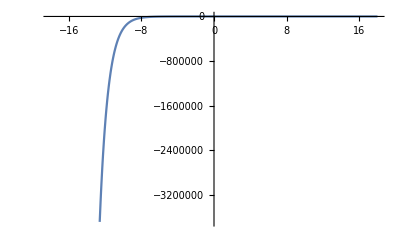

```mathematica
Plot[ⅇ^-x x,{x,-18.,18.}]
```

```mathematica
Integrate[√(2/π)Cos[u t]f[t],{t,0,∞}]
```

∫_0^∞ √(2/π) Cos[t u] f[t]ⅆt

```mathematica
Integrate[√(2/π)Cos[u t]Identity[t],{t,0,∞}]
```

ConditionalExpression[ComplexInfinity,Im[u]<0]

```mathematica
Integrate[√(2/π)Cos[u t]Cos[t],{t,0,∞}]
```

$Aborted

```mathematica
Integrate[Exp[-u t]Cos[t],{t,0,∞}]
```

ConditionalExpression[u/(1+u^2),Re[u]>0]

```mathematica
Integrate[Exp[-u t]Cos[t],{t,0,∞},Assumptions->Re[u]>0]
```

u/(1+u^2)

```mathematica
Integrate[Exp[-u t]Sin[t],{t,0,∞},Assumptions->Re[u]>0]
```

1/(1+u^2)

```mathematica
Integrate[Exp[-u t]Sin[t],{t,-∞,∞},Assumptions->Re[u]>0]
```

Integrate::idiv: Integral of ⅇ^(-t u) Sin[t] does not converge on {-∞,∞}.

Integrate[ⅇ^(-t u) Sin[t],{t,-∞,∞},Assumptions→Re[u]>0]

```mathematica
Integrate[Exp[-u t]t,{t,-∞,∞}]
```

Integrate::idiv: Integral of ⅇ^(-t u) t does not converge on {-∞,∞}.

∫_(-∞)^∞ ⅇ^(-t u) tⅆt

```mathematica
LaplaceTransform[t,t,s]
```

1/s^2

```mathematica
LaplaceTransform[Exp[-t s],t,s]
```

1/(2 s)

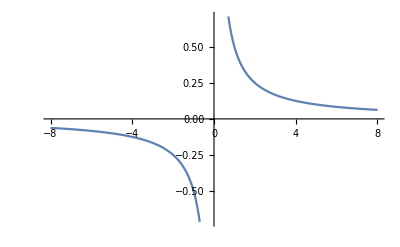

```mathematica
Plot[1/(2 s),{s,-8,8}]
```

```mathematica
LaplaceTransform[Exp'[-t s],t,s]
```

1/(2 s)

```mathematica
ListConvolve[{{1,0,-1},{0,0,0},{-1,0,1}},g]
```

{{-0.00392157,-0.0117647,-0.0117647,0.00392157,0.027451,0.0392157,-7.97973×10^-17,184,-0.00392157,-1.02696×10^-15,-0.0235294,-0.0352941,-0.0156863,3.46945×10^-18,-0.00392157},197}
 |  |  |  |

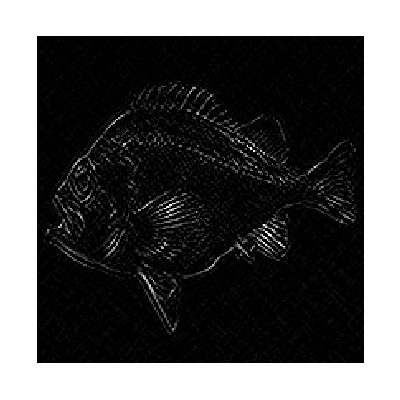

```mathematica
Graphics[Raster[Out[50]]]
```

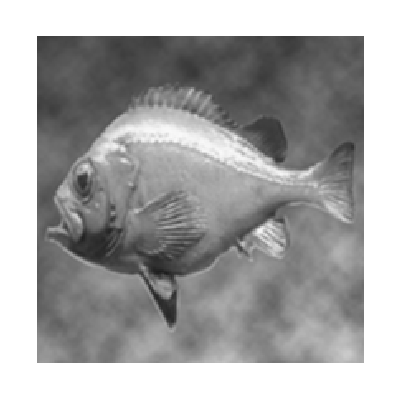

```mathematica
Graphics[Raster[ListConvolve[{{1,2,1},{2,4,2},{1,2,1}}/16,g]]]
```

```mathematica
Graphics[Raster[g]]
```

-Graphics-